# Explorations: Computational Music Workshop

## Megan Davis, adapted by Rory Foulger

## Writing Music in Wolfram Language

### Info: How WL plays sounds

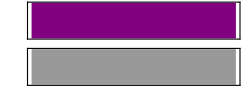

```mathematica
Sound[SoundNote["C"]]
```

```mathematica
Sound[SoundNote[5]]
```

-Graphics-

### Info: Visualizing Scales

I have constructed the major scales on a piano below

!! Note !!
In Wolfram Language, middle C is note 0 and each 1/2 step is equivalent to an increase by 1.
So if C is 0 then C# is 1 and D is 2 etc.

```mathematica
cMaj={0,2,4,5,7,9,11,12};
dMaj={2,4,6,7,9,11,13,14};
eMaj={4,6,8,9,11,13,15,16};
fMaj={5,7,9,10,12,14,16,17};
gMaj={7,9,11,12,14,16,18,19};
aMaj={9,11,13,14,16,18,20,21};
bMaj={11,13,15,16,18,20,22,23};
```

Then we can quickly hear what they sound like and see how Wolfram Language visualizes SoundNotes.

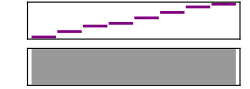

```mathematica
Sound[SoundNote[#,1/4]&/@cMaj,{0,2}]
```

### Task: Write Some Music

#### Example: It’s the Flintstones

Bar code

```mathematica
b1={Sound[SoundNote[12],{0,.5}],Sound[SoundNote[5],{.5,.75}]};
b2={Sound[SoundNote[17],{1.25,1.75}],Sound[SoundNote[14],{1.75,2}]};
b3={Sound[SoundNote[12],{2,2.5}],Sound[SoundNote[5],{2.5,2.75}]};
b4={Sound[SoundNote[12],{3.25,3.75}],Sound[SoundNote[10],{3.75,4}]};
b5={Sound[SoundNote[9],{4,4.25}],Sound[SoundNote[9],{4.25,4.5}],Sound[SoundNote[10],{4.5,4.75}],Sound[SoundNote[12],{4.75,5}]};
b6={Sound[SoundNote[5],{5,5.5}],Sound[SoundNote[7],{5.5,6}]};
b7={Sound[SoundNote[9],{6,6.5}]};
b9={Sound[SoundNote[12],{8,8.5}],Sound[SoundNote[5],{8.5,8.75}]};
b10={Sound[SoundNote[17],{9.25,9.75}],Sound[SoundNote[14],{9.75,10}]};
b11={Sound[SoundNote[12],{10,10.5}],Sound[SoundNote[5],{10.5,10.75}]};
b12={Sound[SoundNote[12],{11.25,11.75}],Sound[SoundNote[10],{11.75,12}]};
b13={Sound[SoundNote[9],{12,12.25}],Sound[SoundNote[9],{12.25,12.5}],Sound[SoundNote[10],{12.5,12.75}],Sound[SoundNote[12],{12.75,13}]};
b14={Sound[SoundNote[5],{13,13.5}],Sound[SoundNote[7],{13.5,14}]};
b15={Sound[SoundNote[5],{14,14.5}]};
b17={Sound[SoundNote[16],{16,16.5}],Sound[SoundNote[9],{16.5,17}]};
b18={Sound[SoundNote[17],{17.25,17.75}],Sound[SoundNote[16],{17.75,18}]};
b19={Sound[SoundNote[16],{18,18.25}],Sound[SoundNote[14],{18.25,18.5}],Sound[SoundNote[14],{18.5,18.75}],Sound[SoundNote[16],{18.75,19}]};
b20={Sound[SoundNote[14],{19,19.25}]};
b21={Sound[SoundNote[14],{20,20.5}],Sound[SoundNote[7],{20.5,21}]};
b22={Sound[SoundNote[16],{21.25,21.75}],Sound[SoundNote[14],{21.75,22}]};
b23={Sound[SoundNote[14],{22,22.25}],Sound[SoundNote[12],{22.25,22.5}],Sound[SoundNote[12],{22.5,22.75}],Sound[SoundNote[14],{22.75,23}]};
b24={Sound[SoundNote[12],{23,23.25}]};
b25={Sound[SoundNote[12],{24,24.5}],Sound[SoundNote[5],{24.5,25}]};
b26={Sound[SoundNote[17],{25.25,25.75}],Sound[SoundNote[14],{25.75,26}]};
b27={Sound[SoundNote[12],{26,26.5}],Sound[SoundNote[5],{26.5,26.75}]};
b28={Sound[SoundNote[12],{27.25,27.75}],Sound[SoundNote[10],{27.75,28}]};
b29={Sound[SoundNote[9],{28,28.25}],Sound[SoundNote[9],{28.25,28.5}],Sound[SoundNote[10],{28.5,28.75}],Sound[SoundNote[12],{28.75,29}]};
b30={Sound[SoundNote[5],{29,29.5}],Sound[SoundNote[7],{29.5,30}]};
b31={Sound[SoundNote[9],{30.125,30.5}],Sound[SoundNote[10],{30.5,30.75}],Sound[SoundNote[12],{30.75,31}]};
b32={Sound[SoundNote[5],{31,31.5}],Sound[SoundNote[7],{31.5,32}]};
b33={Sound[SoundNote[9],{32.25,32.5}],Sound[SoundNote[10],{32.5,32.75}],Sound[SoundNote[12],{32.75,33}]};
b34={Sound[SoundNote[17],{33,33.5}],Sound[SoundNote[19],{33.5,34}]};
b35={Sound[SoundNote[17],{34,35}]};
```

Phrases

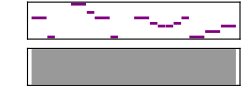

```mathematica
p1=Flatten@{b1,b2,b3,b4,b5,b6,b7};
Sound@p1
```

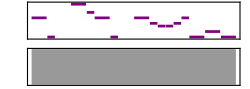

```mathematica
p2=Flatten@{b9,b10,b11,b12,b13,b14,b15};
Sound@p2
```

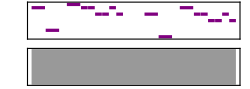

```mathematica
p3=Flatten@{b17,b18,b19,b20,b21,b22,b23,b24};
Sound@p3
```

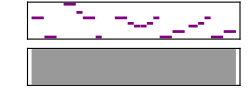

```mathematica
p4=Flatten@{b25,b26,b27,b28,b29,b30,b31,b32};
Sound@p4
```

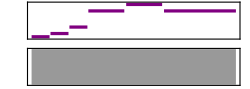

```mathematica
p5=Flatten@{b33,b34,b35};
Sound@p5
```

It’s the Flintstones song! Wow!

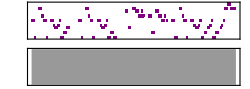

```mathematica
Sound[Flatten@{p1,p2,p3,p4,p5}]
```

#### Example: Scooby Doo

Bar code

```mathematica
B1={Sound[SoundNote[13],{0,.25}],Sound[SoundNote[13],{.25,.5}],Sound[SoundNote[11],{.5,.75}],Sound[SoundNote[11],{.75,1}],Sound[SoundNote[9],{1,2}]};
B2={Sound[SoundNote[11],{2,2.25}],Sound[SoundNote[13],{2.25,3}],Sound[SoundNote[6],{3,3.75}],Sound[SoundNote[6],{3.75,4}]};
B3={Sound[SoundNote[4],{4,4.25}],Sound[SoundNote[4],{4.25,4.5}],Sound[SoundNote[None],{4.5,4.75}],Sound[SoundNote[13],{4.75,5.5}],Sound[SoundNote[11],{5.5,5.75}],Sound[SoundNote[11],{5.75,6}]};
B4={Sound[SoundNote[9],{6,8}]};
B5={Sound[SoundNote[13],{8,8.25}],Sound[SoundNote[13],{8.25,8.5}],Sound[SoundNote[11],{8.5,8.75}],Sound[SoundNote[11],{8.75,9}],Sound[SoundNote[9],{9,10}]};
B6={Sound[SoundNote[11],{10,10.25}],Sound[SoundNote[13],{10.25,11}],Sound[SoundNote[14],{11,11.75}],Sound[SoundNote[6],{11.75,12}]};
B7={Sound[SoundNote[4],{12,12.25}],Sound[SoundNote[4],{12.25,12.5}],Sound[SoundNote[None],{12.5,12.75}],Sound[SoundNote[13],{12.75,13.5}],Sound[SoundNote[11],{13.5,13.75}],Sound[SoundNote[11],{13.75,14}]};
B8={Sound[SoundNote[9],{14,16}]};
B9={Sound[SoundNote[13],{16,16.25}],Sound[SoundNote[13],{16.25,16.5}],Sound[SoundNote[11],{16.5,16.75}],Sound[SoundNote[11],{16.75,17}],Sound[SoundNote[9],{17,18}]};
B10={Sound[SoundNote[11],{18,18.25}],Sound[SoundNote[13],{18.25,19}],Sound[SoundNote[6],{19,19.75}],Sound[SoundNote[6],{19.75,20}]};
B11={Sound[SoundNote[4],{20,20.25}],Sound[SoundNote[4],{20.25,20.5}],Sound[SoundNote[4],{20.5,20.75}],Sound[SoundNote[13],{20.75,21.5}],Sound[SoundNote[11],{21.5,21.75}],Sound[SoundNote[11],{21.75,22}]};
B12={Sound[SoundNote[13],{22,23.75}],Sound[SoundNote[4],{23.75,24}]};
B13={Sound[SoundNote[13],{24,24.25}],Sound[SoundNote[13],{24.25,24.5}],Sound[SoundNote[11],{24.5,24.75}],Sound[SoundNote[11],{24.75,25}],Sound[SoundNote[9],{25,26}]};
B14={Sound[SoundNote[11],{26,26.25}],Sound[SoundNote[13],{26.25,27}],Sound[SoundNote[14],{27,27.75}],Sound[SoundNote[6],{27.75,28}]};
B15={Sound[SoundNote[4],{28,28.25}],Sound[SoundNote[4],{28.25,28.5}],Sound[SoundNote[None],{28.5,28.75}],Sound[SoundNote[13],{28.75,29.5}],Sound[SoundNote[11],{29.5,29.75}],Sound[SoundNote[11],{29.75,30}]};
B16={Sound[SoundNote[9],{30,32}]};
B17={Sound[SoundNote[9],{32,32.25}],Sound[SoundNote[11],{32.25,32.5}],Sound[SoundNote[13],{32.5,32.75}],Sound[SoundNote[14],{32.75,33}],Sound[SoundNote[13],{33,33.25}],Sound[SoundNote[14],{33.25,33.5}],Sound[SoundNote[13],{33.5,33.75}],Sound[SoundNote[14],{33.75,34}]};
B18={Sound[SoundNote[13],{34,34.25}],Sound[SoundNote[14],{34.25,34.5}],Sound[SoundNote[13],{34.5,34.75}],Sound[SoundNote[14],{34.75,35}],Sound[SoundNote[13],{35,35.25}],Sound[SoundNote[14],{35.25,35.5}],Sound[SoundNote[13],{35.5,35.75}],Sound[SoundNote[14],{35.75,36}]};
B19={Sound[SoundNote[14],{36,36.25}],Sound[SoundNote[14],{36.25,36.5}],Sound[SoundNote[14],{36.5,36.75}],Sound[SoundNote[13],{36.75,37}],Sound[SoundNote[None],{37,37.5}],Sound[SoundNote[16],{37.5,38}]};
B20={Sound[SoundNote[16],{38,38.5}],Sound[SoundNote[13],{38.5,40}]};
B21={Sound[SoundNote[9],{40,40.25}],Sound[SoundNote[11],{40.25,40.5}],Sound[SoundNote[13],{40.5,40.75}],Sound[SoundNote[14],{40.75,41}],Sound[SoundNote[13],{41,41.25}],Sound[SoundNote[14],{41.25,41.5}],Sound[SoundNote[13],{41.5,41.75}],Sound[SoundNote[14],{41.75,42}]};
B22={Sound[SoundNote[13],{42,42.25}],Sound[SoundNote[14],{42.25,42.5}],Sound[SoundNote[13],{42.5,42.75}],Sound[SoundNote[14],{42.75,43}],Sound[SoundNote[13],{43,43.25}],Sound[SoundNote[14],{43.25,43.5}],Sound[SoundNote[13],{43.5,43.75}],Sound[SoundNote[14],{43.75,44}]};
B23={Sound[SoundNote[15],{44,44.5}],Sound[SoundNote[16],{44.5,45}],Sound[SoundNote[None],{45,46}]};
B24={Sound[SoundNote[None],{46,46.25}],Sound[SoundNote[16],{46.25,46.5}],Sound[SoundNote[None],{46.5,46.75}],Sound[SoundNote[16],{46.75,47}],Sound[SoundNote[16],{47,48}]};
B25={Sound[SoundNote[13],{48,48.25}],Sound[SoundNote[13],{48.25,48.5}],Sound[SoundNote[11],{48.5,48.75}],Sound[SoundNote[11],{48.75,49}],Sound[SoundNote[9],{49,50}]};
B26={Sound[SoundNote[11],{50,50.25}],Sound[SoundNote[13],{50.25,51}],Sound[SoundNote[6],{51,51.75}],Sound[SoundNote[6],{51.75,52}]};
B27={Sound[SoundNote[4],{52,52.25}],Sound[SoundNote[4],{52.25,52.5}],Sound[SoundNote[None],{52.5,52.75}],Sound[SoundNote[13],{52.75,53.5}],Sound[SoundNote[11],{53.5,53.75}],Sound[SoundNote[11],{53.75,54}]};
B28={Sound[SoundNote[13],{54,55.75}],Sound[SoundNote[9],{55.75,56}]};
B29={Sound[SoundNote[13],{56,56.25}],Sound[SoundNote[13],{56.25,56.5}],Sound[SoundNote[11],{56.5,56.75}],Sound[SoundNote[11],{56.75,57}],Sound[SoundNote[9],{57,58}]};
B30={Sound[SoundNote[11],{58,58.25}],Sound[SoundNote[13],{58.25,59}],Sound[SoundNote[14],{59,59.75}],Sound[SoundNote[6],{59.75,60}]};
B31={Sound[SoundNote[4],{60,60.25}],Sound[SoundNote[4],{60.25,60.5}],Sound[SoundNote[None],{60.5,60.75}],Sound[SoundNote[13],{60.75,61.5}],Sound[SoundNote[11],{61.5,61.75}],Sound[SoundNote[11],{61.75,62}]};
B32={Sound[SoundNote[9],{62,64}]};
```

Phrases

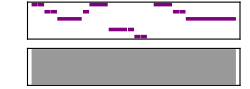

```mathematica
sd1=Flatten@{B1,B2,B3,B4};
Sound@sd1
```

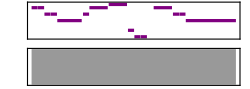

```mathematica
sd2=Flatten@{B5,B6,B7,B8};
Sound@sd2
```

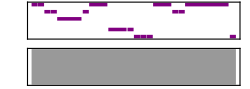

```mathematica
sd3=Flatten@{B9,B10,B11,B12};
Sound@sd3
```

```mathematica
sd4=Flatten@{B13,B14,B15,B16};
Sound@sd4
```

-Graphics-

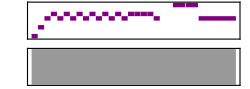

```mathematica
sd5=Flatten@{B17,B18,B19,B20};
Sound@sd5
```

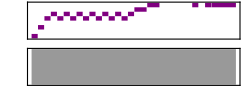

```mathematica
sd6=Flatten@{B21,B22,B23,B24};
Sound@sd6
```

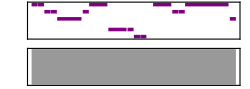

```mathematica
sd7=Flatten@{B25,B26,B27,B28};
Sound@sd7
```

```mathematica
sd8=Flatten@{B29,B30,B31,B32};
Sound@sd8
```

-Graphics-

Full Song

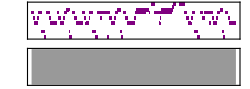

```mathematica
Sound@Flatten@{sd1,sd2,sd3,sd4,sd5,sd6,sd7,sd8}
```

Now go forth and create something! Create your very own composition with the musical concepts and sounds in the Wolfram Language, or try to recreate a song you know with sounds!

#### Mini Task: Here’s a phrase from Frozen’s Let it Go - try to make it sound like the real thing.

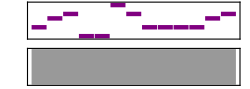

```mathematica
Sound[{SoundNote["F"],SoundNote["G"],SoundNote["GSharp"],SoundNote["DSharp"],SoundNote["DSharp"],SoundNote["ASharp"],
SoundNote["GSharp"],SoundNote["F"],SoundNote["F"],SoundNote["F"],SoundNote["F"],SoundNote["G"],SoundNote["GSharp"]
}]
```

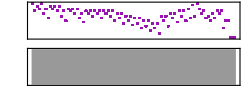

```mathematica
noteList={0, -5, -2, -4, 0, -7, -4, -10, -2, -4, -2, -5, -2, -9, -5, -12, -4, -5, -4, -7, -4, -10,-7, -13, -5, -7, -5, -9, -5, -7, -5, -10, -5,-7,-5, -9, -5, -12, -7, -10, -7, -14, -9, -12, -9, -15, -10,-14, -10, -17, -12, -16, -12, -19, -14, -17, -14, -21, -9, -12, -9, -16, -7, -10, -7, -13, -5, -9, -5, -12, -4, -10, -1, -9, 0, -4, -7, -5, -10, -9, -12, -7, -10, -5, -7, -5, -17, -12, -12, -24,-24, -24 } ;
notes=SoundNote[#, 1/5, "Organ"]&/@noteList;
Sound[notes]
```

## Computational Music

### Task 1: Play bubble sort in sort

Implement a bubble sort in WL

Find the steps the bubble sort took

Play a ping every time the bubble sort returns to the start of the list

Translate into sound

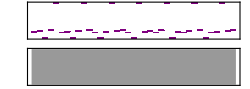

#### Hint 1:

you’ll need a list of numbers

```mathematica
data=RandomInteger[{-5,5},5]
```

{-5,2,2,-2,-4}

#### Hint 2:

Use some replacement functions and patterns to make a bubble sort. Stack exchange is your best friend.

```mathematica
bubbleSort=data//.{a___,b_,c_,d___}/;b>c->{a,c,b,d}
```

{-5,-4,-2,2,2}

#### Hint 3:

Make a pure function which gets you the steps

```mathematica
sortstep:=#/. {a___,b_,c_,d___}/;b>c->{a,c,b,d}&
```

#### Hint 4:

make a list of the steps taken using NestWhileList

```mathematica
sorted=Most[NestWhileList[sortstep,data,UnsameQ[##]&,2]];
```

#### Hint 5:

Insert a tone at the end of every list

```mathematica
tone=Flatten@sorted
```

{-5,2,2,-2,-4,-5,2,-2,2,-4,-5,-2,2,2,-4,-5,-2,2,-4,2,-5,-2,-4,2,2,-5,-4,-2,2,2}

#### Hint 6:

Play the sound

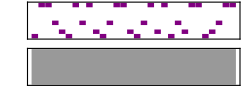

```mathematica
Sound[Table[SoundNote[i,0.1],{i,tone}]]
```

### Task 2: play a different algorithm

{24,12,29,6,19,3,15,8,30,13,17,18,11,21,14,9,5,25,7,26,22,28,10,4,23,20,2,1,27,16}

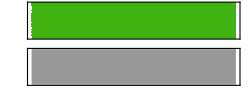

```mathematica
l=RandomSample[Range[30], 30]
sorted=NestWhileList[sortstep,l,UnsameQ[##]&,2];
tone = Flatten@sorted;
Sound[Table[SoundNote[i,0.1, "Marimba", SoundVolume->1/3],{i,tone}], 30]
```

```mathematica
h
```

## Further Reading

https://www.pianoscales.org/
Abstract Algebra 3rd Ed. by Dummit and Foote (classic abstract algebra book)

Inspirations
Quadrivium talk via MoMath with Marcus G Miller and Stephon Alexander
Listening to  SO MUCH jazz music and finding SO MANY patterns
Legit talking to professional musicians

Other Readings
https://www.bbc.com/news/entertainment-arts-50335897
http://dadabots.com/
https://www.bbc.com/news/technology-20889644
https://computerhistory.org/blog/algorithmic-music-david-cope-and-emi/
https://www.aiva.ai/

Of course there is also:
https://tones.wolfram.com/generate/GU1Rr5SCJghGc4AK0DpeKgH4kKJAOG2LHo61sYZs9rEZr

```mathematica
Import["Test.midi"]
```

Import::nffil: File Test.midi not found during Import.

$Failed

```mathematica
Import["\"C:\\Users\\chris\\Downloads\\jsbwv549.mid\""]
```

Import::nffil: File "C:\Users\chris\Downloads\jsbwv549.mid" not found during Import.

$Failed

```mathematica
InputForm[Import["C:\\Users\\chris\\Downloads\\jsbwv549.mid"]]
```

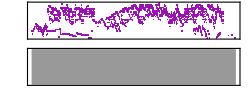

```mathematica
%
```

```mathematica
Audio[Array[Sin[2 π 440 #]&,44100,{0,1}]]
Sound[Array[Sin[2 π 440 #]&,44100,{0,1}]]
```

```mathematica
Sound[{Play[SquareWave[400t],{t,0,.2}]}]
```

-Graphics-

```mathematica
l=
```

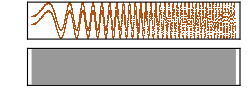

```mathematica
noteList = Round/@N[20*Sin[#^2/10000]&]/@Range[1500];
notes=SoundNote[#, 1/10, "Crystal"]&/@Transpose[{noteList, noteList+12}];
Sound[notes]
```

```mathematica
topNote=20;
bottomNote=-20;
noteList=Table[Range[bottomNote, topNote, 12]+Mod[n, 12], {n, 0, 200}] 
noteList=Table[Table[]]
```

Range::range: Range specification in Range[Null,100,12] does not have appropriate bounds.

-Graphics-

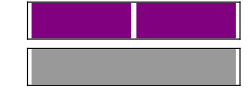

{{{0.2,SoundNote[A]},{0.5,SoundNote[C]}},{{0.5,SoundNote[A]},{0.2,SoundNote[C]}}}

```mathematica
Sound[{{Sound[SoundNote["A"], SoundVolume->1/4]}, {Sound[SoundNote["A"], SoundVolume->1]}}]
Audio[0.2*AudioData[Sound[SoundNote["A"]]]+AudioData[Sound[SoundNote["C"]]]]
l={{{0.2, SoundNote["A"]}, {0.5, SoundNote["C"]}}, {{0.5, SoundNote["A"]}, {0.2, SoundNote["C"]}}}

AudioJoin[Audio[Plus@@(#[[1]]*AudioData[Sound[#[[2]]]]&/@#)]&/@l]
```